## 1 - XXZ Hamiltonian with open boundary conditions

```mathematica
(* H = J Sum[Sx_j Sx_(j+1) + Sy_j Sy_(j+1) + delta Sz_j Sz_(j+1)].
   S = sigma/2; hbar = 1; J and delta are real; L >= 1.
   Basis: {|0...0>, ..., |1...1>}, with site 1 the leftmost factor.
   Z|0> = |0>, Z|1> = -|1>. *)

ClearAll[XXZHamiltonian];

XXZHamiltonian[j_, anisotropy_, n_Integer] /; n >= 1 := Module[{bond, h},
  bond = SparseArray[j/4 {{anisotropy, 0, 0, 0},
    {0, -anisotropy, 2, 0}, {0, 2, -anisotropy, 0},
    {0, 0, 0, anisotropy}}];
  h = SparseArray[{}, {2^n, 2^n}];
  Do[h += KroneckerProduct[IdentityMatrix[2^(k - 1), SparseArray],
    bond, IdentityMatrix[2^(n - k - 1), SparseArray]], {k, 1, n - 1}];
  h
];
```

### Parameters

```mathematica
L = 4;
J = 1.;
delta = 0.5;
H = XXZHamiltonian[J, delta, L];
```

```mathematica
H//MatrixForm
```

(0.375 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.125 | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.5 | -0.125 | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.125 | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.5 | 0. | -0.125 | 0. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.5 | 0. | -0.375 | 0.5 | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.5 | -0.125 | 0. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.125 | 0. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0.125 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.5 | 0. | 0. | 0. | -0.125 | 0.5 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.5 | 0. | 0. | 0.5 | -0.375 | 0. | 0.5 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.5 | 0. | 0. | 0. | -0.125 | 0. | 0.5 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.5 | 0. | 0.125 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.5 | 0. | -0.125 | 0.5 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.5 | 0.125 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.375)

### Numerical unit tests

```mathematica
(* Fixed small test cases; independent of the parameters above.
   The three-spin reference uses {|100>, |010>, |001>}.
   Dense conversion is confined to these small tests. *)

Module[{hTest, uTest, up, oneDown, tolerance = 10^-12},
  hTest = XXZHamiltonian[1.3, 0.7, 5];
  uTest = MatrixExp[-I 0.37 Normal[hTest]];
  up = UnitVector[32, 1];
  oneDown = Normal[XXZHamiltonian[1.3, 0.7, 3][[{5, 3, 2}, {5, 3, 2}]]];

  TestReport[{
    VerificationTest[{Head[hTest], Dimensions[hTest]}, {SparseArray, {32, 32}},
      TestID -> "Sparse matrix and dimension"],
    VerificationTest[Norm[hTest - ConjugateTranspose[hTest], "Frobenius"] < tolerance,
      True, TestID -> "Hermiticity"],
    VerificationTest[Norm[oneDown - 0.65 {{0, 1, 0}, {1, -0.7, 1}, {0, 1, 0}},
      "Frobenius"] < tolerance, True, TestID -> "Open boundaries and bond normalization"],
    VerificationTest[Norm[hTest . up - 0.91 up] < tolerance,
      True, TestID -> "Polarized-state energy: J delta (L-1)/4"],
    VerificationTest[Norm[ConjugateTranspose[uTest] . uTest - IdentityMatrix[32],
      "Frobenius"] < tolerance, True, TestID -> "Unitary time evolution"]
  }]
]
```

TestReportObject[…]

## 2 - Magnetization sectors and eigenvectors

```mathematica
(* Sz = Sum[Z_j]/2. A basis state with r down spins has Sz = L/2 - r.
   Each sector contains Binomial[L, r] computational basis states.
   Basis indices are one-based, as in Mathematica. *)

ClearAll[TotalMagnetization, MagnetizationSectors, MagnetizationEigensystem];

TotalMagnetization[n_Integer] /; n >= 1 := SparseArray[
  Band[{1, 1}] -> Table[n/2 - DigitCount[b, 2, 1], {b, 0, 2^n - 1}],
  {2^n, 2^n}];

MagnetizationSectors[n_Integer] /; n >= 1 :=
  GroupBy[Range[2^n], n/2 - DigitCount[# - 1, 2, 1] &];

MagnetizationEigensystem[h_, groups_Association] := SortBy[
  Flatten[KeyValueMap[Function[{m, indices}, Module[{e, v},
    {e, v} = Eigensystem[Normal[N[h[[indices, indices]]]]];
    MapThread[<|"Energy" -> #1, "Magnetization" -> m,
      "Vector" -> SparseArray[Thread[indices -> #2], {Length[h]}]|> &, {e, v}]
  ]], groups], 1], #["Energy"] &];
```

### Build sectors and diagonalize H

```mathematica
Sz = TotalMagnetization[L];
sectors = MagnetizationSectors[L];
sectorDimensions = Length /@ sectors;
eigenstates = MagnetizationEigensystem[H, sectors];
```

```mathematica
(* eigenstates[[k]] contains the kth energy, magnetization, and full vector.
   States are sorted by increasing energy. Diagonalizing each block avoids
   mixing different magnetizations when their energies are degenerate. *)

Grid[Prepend[KeyValueMap[{#1, #2} &, sectorDimensions],
  {"Magnetization", "Sector dimension"}], Frame -> All]

eigenstateTable = MapIndexed[<|"State" -> First[#2],
  "Energy" -> #1["Energy"], "Magnetization" -> #1["Magnetization"]|> &, eigenstates];
Dataset[eigenstateTable]
```

Magnetization | Sector dimension
2 | 1
1 | 4
0 | 6
-1 | 4
-2 | 1

```mathematica
eigenstateTable = SortBy[
  MapIndexed[
    <|"State" -> First[#2], "Energy" -> #1["Energy"],
      "Magnetization" -> #1["Magnetization"]|> &, eigenstates],
  {-#["Magnetization"] &, #["Energy"] &}
];
Dataset[eigenstateTable]
```

### Numerical tests of the sector decomposition

```mathematica
Module[{tolerance = 10^-12},
  TestReport[{
    VerificationTest[Norm[H . Sz - Sz . H, "Frobenius"] < tolerance,
      True, TestID -> "Total magnetization is conserved"],
    VerificationTest[Sort[Join @@ Values[sectors]], Range[2^L],
      TestID -> "Sectors partition the full basis"],
    VerificationTest[Values[sectorDimensions],
      Binomial[L, L/2 - #] & /@ Keys[sectors], TestID -> "Sector dimensions"],
    VerificationTest[Length[eigenstates], 2^L, TestID -> "Complete eigensystem"],
    VerificationTest[Max[Norm[H . #["Vector"] - #["Energy"] #["Vector"]] & /@
      eigenstates] < tolerance, True, TestID -> "Hamiltonian eigenvector residuals"],
    VerificationTest[Max[Norm[Sz . #["Vector"] - #["Magnetization"] #["Vector"]] & /@
      eigenstates] < tolerance, True, TestID -> "Definite magnetization of every eigenvector"]
  }]
]
```

TestReportObject[…]

## 3 - Spectrum versus anisotropy, colored by magnetization

### Anisotropy range

```mathematica
L=6;
deltaMin = -2;
deltaMax = 2;
deltaStep = 1/50;
deltaList = N[Range[deltaMin, deltaMax, deltaStep]];
```

### Compute the spectrum in each sector

```mathematica
(* H(delta) = Hxy + delta Hz. Build these matrices once.
   Each row of sectorSpectrum[m] contains the sorted energies at one delta.
   Only eigenvalues are needed for this plot. *)

Hxy = XXZHamiltonian[J, 0, L];
Hz = XXZHamiltonian[J, 1, L] - Hxy;
spectrumSectors = MagnetizationSectors[L];

sectorSpectrum = Association[KeyValueMap[Function[{m, indices},
  m -> Module[{a = Normal[N[Hxy[[indices, indices]]]],
    b = Normal[N[Hz[[indices, indices]]]]},
    Table[Sort[Eigenvalues[a + d b]], {d, deltaList}]
  ]], spectrumSectors]];
```

### Plot all levels

```mathematica
magnetizations = Keys[sectorSpectrum];

sectorColors = AssociationThread[magnetizations,
  Table[Hue[Mod[(k - 1)/N[GoldenRatio], 1], 0.75, 0.8],
    {k, Length[magnetizations]}]];

sectorStyles = Table[
  Directive[sectorColors[m], AbsoluteThickness[1.5],
    If[m < 0, Dashed, Dashing[{}]]],
  {m, magnetizations}];

levelCurves = Flatten[Table[
  Transpose[{deltaList, #}] & /@ Transpose[sectorSpectrum[m]],
  {m, magnetizations}], 1];
levelStyles = Flatten[Table[ConstantArray[sectorStyles[[k]],
  Length[spectrumSectors[magnetizations[[k]]]]],
  {k, Length[magnetizations]}], 1];
```

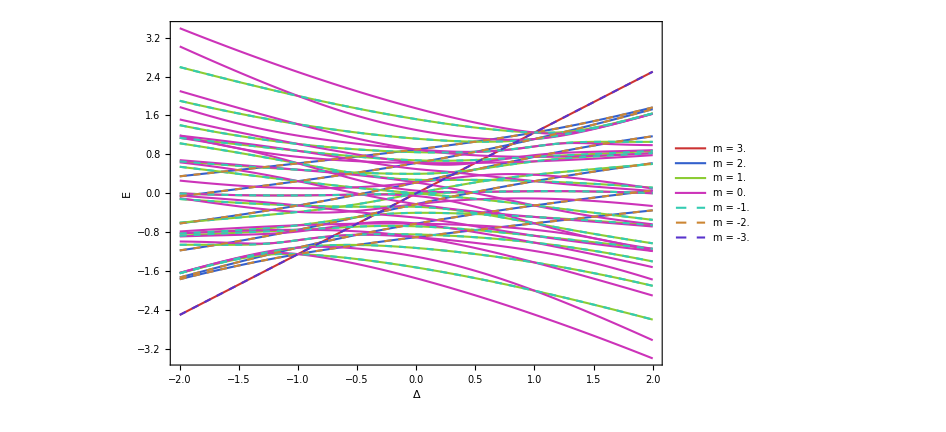

```mathematica
(* Spin-flip symmetry makes the spectra at m and -m coincide.
   Negative sectors are dashed and drawn over the solid positive sectors.
   Curves connect energies in ascending order within each sector. *)

spectrumPlot = ListLinePlot[levelCurves, PlotStyle -> levelStyles,
  Frame -> True, Axes -> False, FrameLabel -> {"Δ", "E"},
  PlotLegends -> Placed[LineLegend[sectorStyles,
    Row[{"m = ", N[#]}] & /@ magnetizations], Right],
  PlotRange -> All, ImageSize -> 700];
spectrumPlot
```

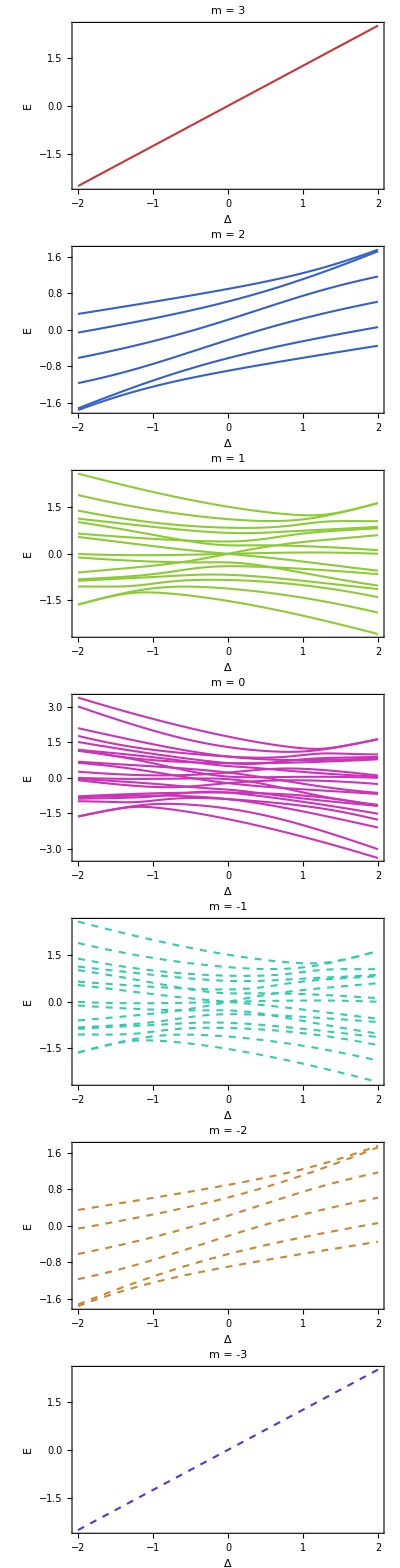

```mathematica
Column[
 MapThread[
  Function[{m, style},
   ListLinePlot[
    (Transpose[{deltaList, #}] &) /@ Transpose[sectorSpectrum[m]],
    PlotStyle -> style,
    Frame -> True,
    Axes -> False,
    FrameLabel -> {"Δ", "E"},
    PlotLabel -> Row[{"m = ", m}],
    PlotRange -> All,
    ImageSize -> Large
    ]
   ],
  {magnetizations, sectorStyles}
  ],
 Spacings -> 2
 ]
```

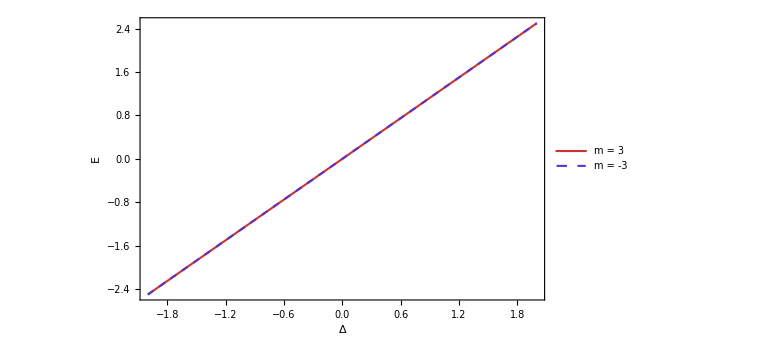
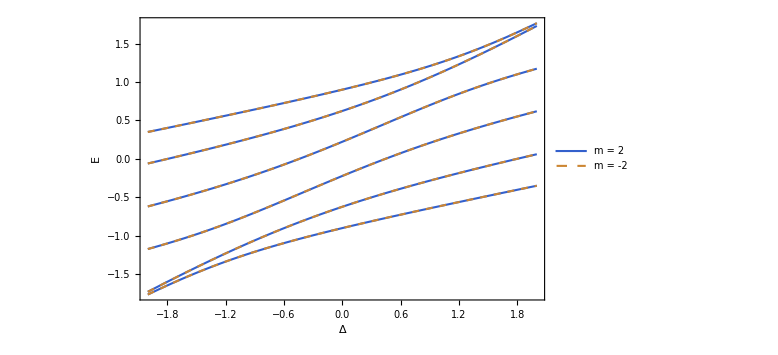
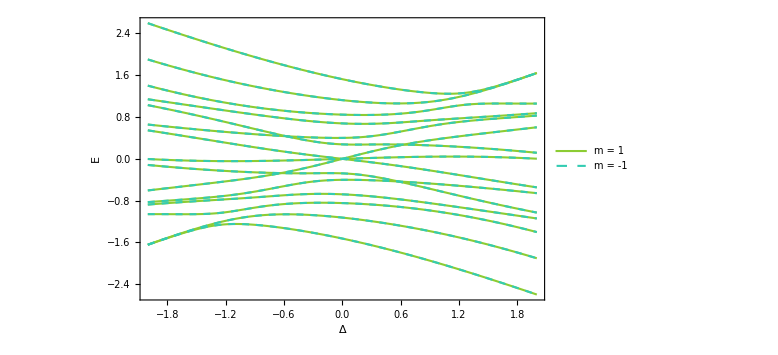
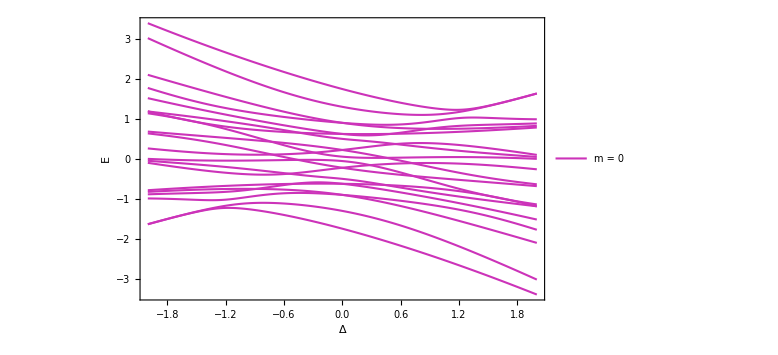

```mathematica
sectorStyleMap = AssociationThread[magnetizations, sectorStyles];

Column[
 Table[
  With[{sectors = If[m == 0, {0}, {m, -m}]},
   ListLinePlot[
    Flatten[
     Table[
      (Transpose[{deltaList, #}] &) /@ Transpose[sectorSpectrum[s]],
      {s, sectors}], 1],
    PlotStyle -> Flatten[
      Table[
       ConstantArray[sectorStyleMap[s],
        Length[First[sectorSpectrum[s]]]],
       {s, sectors}], 1],
    PlotLegends -> LineLegend[
      Lookup[sectorStyleMap, sectors],
      (Row[{"m = ", #}] &) /@ sectors],
    Frame -> True,
    Axes -> False,
    FrameLabel -> {"Δ", "E"},
    PlotRange -> All,
    ImageSize -> Large
    ]
   ],
  {m, Select[magnetizations, # >= 0 &]}
  ],
 Spacings -> 2
 ]
```

## Phantom states

```mathematica
ClearAll[SpinHelixState];

SpinHelixState[n_Integer, q_, theta_: Pi/2, phi_: 0] :=
 Flatten[
  KroneckerProduct @@ Table[
    {Cos[theta/2],
     Exp[I (phi + (j - 1) q)] Sin[theta/2]},
    {j, n}
    ]
  ];
```

```mathematica
Dataset[
 Table[
  With[{
    psi = N[SpinHelixState[6, q]],
    h = N[XXZHamiltonian[1, Cos[q], 6]],
    e = N[5 Cos[q]/4]
    },
   <|"q" -> q, "Delta" -> Cos[q],
    "Energy expectation" -> e,
    "Eigenstate residual" -> Chop[Norm[h . psi - e psi]]|>
   ],
  {q, {0, Pi/3, Pi}}
  ]
 ]
```

## Helix states + boundary fields

```mathematica
(* XXZ with endpoint magnetic fields *)

ClearAll[BoundaryField, BoundaryXXZHamiltonian,
  HelixXXZHamiltonian];

BoundaryField[v_List] :=
 SparseArray[Sum[v[[k]] PauliMatrix[k], {k, 3}]/2];

BoundaryXXZHamiltonian[j_, anisotropy_, n_Integer,
   hLeft_List, hRight_List] :=
 XXZHamiltonian[j, anisotropy, n] +
  KroneckerProduct[BoundaryField[hLeft],
   IdentityMatrix[2^(n - 1), SparseArray]] +
  KroneckerProduct[IdentityMatrix[2^(n - 1), SparseArray],
   BoundaryField[hRight]];

HelixXXZHamiltonian[j_, pitch_, n_Integer, phase_: 0,
   bL_: 0, bR_: 0] :=
 With[{a = phase + (n - 1) pitch, c = j Sin[pitch]/2},
  BoundaryXXZHamiltonian[j, Cos[pitch], n,
   -c {-Sin[phase], Cos[phase], 0} +
    bL {Cos[phase], Sin[phase], 0},
   c {-Sin[a], Cos[a], 0} +
    bR {Cos[a], Sin[a], 0}]
  ];
```

```mathematica
(* Example and full diagonalization *)

L = 6;
J = 1.;
helixPitch = Pi/3;
helixPhase = 0;
bLeft = 0.2;
bRight = 0;

Hboundary = HelixXXZHamiltonian[
   J, helixPitch, L, helixPhase, bLeft, bRight];

helixKet = N[SpinHelixState[
    L, helixPitch, Pi/2, helixPhase]];

helixEnergy = J (L - 1) Cos[helixPitch]/4 +
   (bLeft + bRight)/2;
```

```mathematica
{boundaryEnergies, boundaryVectors} =
 Eigensystem[Normal[N[Hboundary]]];
```

```mathematica
Dataset[<|
  "Hermiticity residual" ->
   Chop[Norm[Hboundary - ConjugateTranspose[Hboundary],
     "Frobenius"]],
  "Helix eigenstate residual" ->
   Chop[Norm[Hboundary . helixKet - helixEnergy helixKet]],
  "Magnetization commutator norm" ->
   Norm[Hboundary . TotalMagnetization[L] -
     TotalMagnetization[L] . Hboundary, "Frobenius"]
  |>]
```

```mathematica
spinFlipX =
 KroneckerProduct @@ ConstantArray[PauliMatrix[1], L];

helixProjector =
 Outer[Times, helixKet, Conjugate[helixKet]];

Chop[{
  Norm[Hboundary -
    spinFlipX . Conjugate[Hboundary] . spinFlipX, "Frobenius"],
  Norm[Hboundary . helixProjector -
    helixProjector . Hboundary, "Frobenius"]
  }]
```

{0,0}

## Particular helix states

```mathematica
L = 8;
J = 1.;
pitch = 0.7;
anisotropy = Cos[pitch];

c = J Sin[pitch]/2;
b = -c Cot[(L - 1) pitch/2];
endpointField = {b, -c, 0};

h0 = Normal[N[XXZHamiltonian[J, anisotropy, L]]];

hExact = Normal[N[
    BoundaryXXZHamiltonian[
     J, anisotropy, L, endpointField, endpointField]]];

hEdge = hExact - h0;
```

```mathematica
helixPlus = N[SpinHelixState[L, pitch, Pi/2, 0]];
helixMinus =
  N[SpinHelixState[L, -pitch, Pi/2, (L - 1) pitch]];

lambdaList = Subdivide[0., 1.5, 300];
```

```mathematica
spectrum = Table[
   Sort[Re[Chop[Eigenvalues[h0 + lambda hEdge]]]],
   {lambda, lambdaList}];
```

```mathematica
trialEnergy[lambda_] :=
  J (L - 1) anisotropy/4 + lambda b;

residuals = Table[
   With[{h = h0 + lambda hEdge, e = trialEnergy[lambda]},
    {lambda,
     Norm[h . helixPlus - e helixPlus],
     Norm[h . helixMinus - e helixMinus]}],
   {lambda, lambdaList}];
```

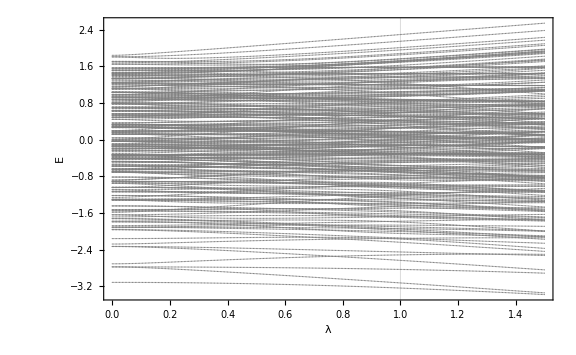
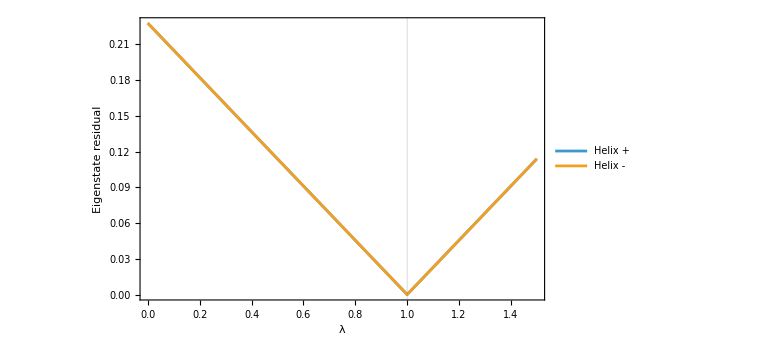

```mathematica
Column[{
  ListPlot[
   (Transpose[{lambdaList, #}] &) /@ Transpose[spectrum],
   Frame -> True, Axes -> False,
   FrameLabel -> {"λ", "E"},
   PlotStyle -> Directive[Gray, PointSize[0.0015]],
   GridLines -> {{1}, None},
   PlotRange -> All, ImageSize -> Large],

  ListLinePlot[
   {residuals[[All, {1, 2}]], residuals[[All, {1, 3}]]},
   Frame -> True, Axes -> False,
   FrameLabel -> {"λ", "Eigenstate residual"},
   PlotLegends -> {"Helix +", "Helix -"},
   GridLines -> {{1}, None},
   PlotRange -> All, ImageSize -> Large]
  }]
```

```mathematica
L = 6;
J = 1.;
pitch = 0.7;
anisotropy = Cos[pitch];

c = J Sin[pitch]/2;
b = -c Cot[(L - 1) pitch/2];
endpointField = {b, -c, 0};

h0 = Normal[N[XXZHamiltonian[J, anisotropy, L]]];

hExact = Normal[N[
    BoundaryXXZHamiltonian[
     J, anisotropy, L, endpointField, endpointField]]];

hEdge = hExact - h0;

helixPlus = N[SpinHelixState[L, pitch, Pi/2, 0]];
helixMinus =
  N[SpinHelixState[L, -pitch, Pi/2, (L - 1) pitch]];

helixEnergy = J (L - 1) anisotropy/4 + b;

(* Projector onto the span of both helices *)
a = Transpose[{helixPlus, helixMinus}];
aDag = ConjugateTranspose[a];
pHelix = a . Inverse[aDag . a] . aDag;

(* Eigensystem at the exact point, sorted by ascending energy *)
{energies, vectors} = Eigensystem[hExact];
order = Ordering[Re[Chop[energies]]];
energies = Re[Chop[energies[[order]]]];
vectors = vectors[[order]];

weights = Chop[
   (Re[Conjugate[#] . pHelix . #] &) /@ vectors];

tolerance = 10^-9;
helixIndices = Select[
   Range[Length[energies]],
   Abs[energies[[#]] - helixEnergy] < tolerance &];

Print[Dataset[
   Table[
    <|"Ascending index" -> n,
     "Energy" -> energies[[n]],
     "Helix-subspace weight" -> weights[[n]]|>,
    {n, helixIndices}]]];

Print["Helix residuals: ",
  Chop[{
    Norm[hExact . helixPlus - helixEnergy helixPlus],
    Norm[hExact . helixMinus - helixEnergy helixMinus]}]];
```

Helix residuals: {0,0}

```mathematica
(* Full spectrum versus boundary-field strength *)
lambdaList = Subdivide[0., 1.5, 600];

spectrum = Table[
   Sort[Re[Chop[Eigenvalues[h0 + lambda hEdge]]]],
   {lambda, lambdaList}];
```

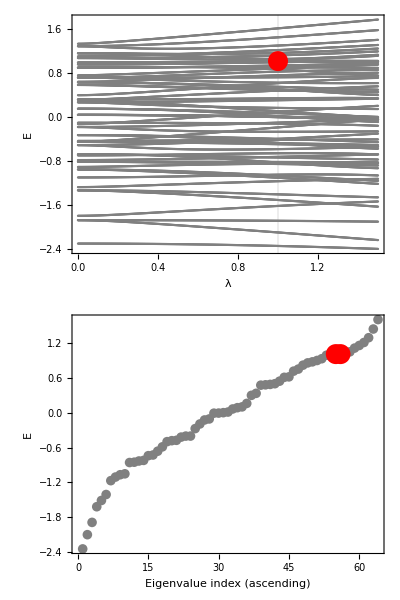

```mathematica
Column[{
  ListPlot[
   (Transpose[{lambdaList, #}] &) /@ Transpose[spectrum],
   Frame -> True, Axes -> False,
   FrameLabel -> {"λ", "E"},
   PlotStyle -> Directive[Gray, PointSize[0.002]],
   GridLines -> {{1}, None},
   Epilog -> {Red, PointSize[0.018],
     Point[{1, helixEnergy}]},
   PlotRange -> All, ImageSize -> 800],

  (* Shows exactly where the helices sit at lambda = 1 *)
  ListPlot[
   Transpose[{Range[Length[energies]], energies}],
   Frame -> True, Axes -> False,
   FrameLabel -> {"Eigenvalue index (ascending)", "E"},
   PlotStyle -> Directive[Gray, PointSize[0.012]],
   Epilog -> {Red, PointSize[0.025],
     Point[Transpose[
       {helixIndices, energies[[helixIndices]]}]]},
   PlotRange -> All, ImageSize -> Large]
  }]
```